# q q̄→μ μ in EW theory (SM ): GENERIC CHARGES

mass leptons MM!=0, box calculation

### PROCESS:

```mathematica
CKM = IndexDelta;
Neglect[MU] = Neglect[MU2] = 0;
(*Neglect[MM] = Neglect[MM2] = 0;*)
process ={F[3, {1}], -F[3, {1}]} -> {F[2, {2}], -F[2, {2}]} ;

SetOptions[InsertFields,  Model -> "SM",InsertionLevel->{Particles}, Restrictions -> NoLightFHCoupling];
(*SetOptions[CalcFeynAmp,PaVeReduce->True];*)
(*SetOptions[CreateFeynAmp, GaugeRules -> {GaugeXi[Z] -> ZGAUGE, GaugeXi[A] -> AGAUGE,
 GaugeXi[W] -> WGAUGE} ];*)
```

## SM: Feynman rules and diagrams

Definisco valori di cariche e masse sostituite poi nei passaggi finali

```mathematica
CHARGESZl={QZLl->-1,QZUl->2/3,QZDl->-1/3,I3D->-1/2,I3L->-1/2,I3N->1/2,I3U->1/2};
CHARGESZr={QZLr->-1,QZUr->2/3,QZDr->-1/3};
CHARGESphl={QLl->-1,QUl->2/3,QDl->-1/3};
CHARGESphr={QLr->-1,QUr->2/3,QDr->-1/3};
MASSES={MU->0,MU2->0,MM->0,MM2->0,MD->0,MD2->0,S+T+U->0}
```

{MU→0,MU2→0,MM→0,MM2→0,MD→0,MD2→0,S+T+U→0}

```mathematica
(*GENERALIZZAZIONE CARICHE/ISOSPIN PER CASO SM*)
coupling[x_]:=Module[{Mcouplin,chargenuZ,chargelepZ,chargeupZ,chargedownZ,n,m,chargenup,chargelep,chargedown,chargeup},

Mcouplin=M$CouplingMatrices;
(*____________________________  Z COUPLING  ______________________________*)
(*neutrino*)
chargenuZ[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[2]])==rhs_]:=
lhs==(rhs/.{
	dZZZ1-> 2 I3N dZZZ1,
	1/(2 CW SW)->I3N/(CW SW),
	EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
	

});
chargenuZ[other_]=other;
Mcouplin=chargenuZ/@Mcouplin;

(*lepton*)
chargelepZ[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3L*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			SW/CW->-QZLl SW/CW,
			(-1/2+SW^2)->(I3L-QZLl*SW^2),
			dZAZ1->- QLl dZAZ1 (*CT misto gamma Z*)
			},
		rhsR/.{
		SW/CW->-QZLr SW/CW,
		dZAZ1->- QLr dZAZ1 (*CT misto gamma Z*)
		}
});
chargelepZ[other_]=other;
Mcouplin=chargelepZ/@Mcouplin;

(*q up*)
chargeupZ[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3U*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(1/2-2/3SW^2)->(I3U-QZUl*SW^2),
			
			dZAZ1->3/2 QUl dZAZ1,(*CT misto gamma Z: − δ [g1,g2] QU δZ(γZ)/2*)
			-2/3->-QZUl},
		rhsR/.{
			-dZAZ1 /3->-QUr*dZAZ1 /2, (*CT misto gamma Z*)
			-1/3 I*EL->-QZUr/2 I*EL,
			-2/3*I->-QZUr*I,
			-2/3->-QZUr,
			-SW /(3*CW)->-QZUr*SW /(2*CW)}
});
chargeupZ[other_]=other;
Mcouplin=chargeupZ/@Mcouplin;

(*q down*)
chargedownZ[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[2]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{
			-(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(2 CW SW)->I3D*(dZe1+(dSW1 (-CW2+SW2))/(CW2 SW))/(CW SW),
			(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),
			dZAZ1->-3 QDl dZAZ1, (*CT misto gamma Z*)
			1/3->-QZDl},
			
		rhsR/.{
			dZZZ1->- 3 QZDr*dZZZ1 ,
			dZAZ1->- 3 QDr*dZAZ1 ,(*CT misto gamma Z*)
			1/3 I*EL->-QZDr I*EL,
			1/3*I->-QZDr*I,
			1/3->-QZDr,
			SW /(3*CW)->-QZDr*SW /(CW)}
});
chargedownZ[other_]=other;
Mcouplin=chargedownZ/@Mcouplin;

(*____________________________  GAMMA COUPLING  ___________________________*)
(*neutrino*)
chargenup[(lhs:C[_. F[1,{__}],_. F[1,{__}],_. V[1]])==rhs_]:=
lhs==(rhs/.{
		EL IndexDelta[j1_,j2_]->2*I3N*EL IndexDelta[j1,j2]
});
chargenup[other_]=other;
Mcouplin=chargenup/@Mcouplin;
(*lepton*)
chargelep[(lhs:C[_. F[2,{__}],_. F[2,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+SW^2)->(I3L-QZLl*SW^2)/-QLl,(*CT misto gamma Z*)
			I->-QLl*I,
			1/2*I->-1/2 QLl*I
},
			
		rhsR/.{dZZA1->- QZLr dZZA1/-QLr,(*CT misto gamma Z*)
		I->-QLr*I,
			1/2*I->-1/2 QLr*I
		}
});
chargelep[other_]=other;
Mcouplin=chargelep/@Mcouplin;

(*q up*)
chargeup[(lhs:C[_. F[3,{__}],_. F[3,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(1/2-2/3SW^2)->(I3U-QZUl*SW^2),(*CT misto gamma Z*)
			-2/3->-QUl,
			-2/3*I->-QUl*I},
			
		rhsR/.{dZZA1->3/2 QZUr dZZA1,(*CT misto gamma Z*)
		-2/3->-QUr,
		-2/3*I->-QUr*I}
});
chargeup[other_]=other;
Mcouplin=chargeup/@Mcouplin;

(*q down*)
chargedown[(lhs:C[_. F[4,{__}],_. F[4,{__}],_. V[1]])=={rhsL_,rhsR_}]:=
lhs==({rhsL/.{(-1/2+1/3 SW^2)->(I3D-QZDl*SW^2),(*CT misto gamma Z*)
			1/3->-QDl,
			1/3*I->-QDl*I
			},
							
	rhsR/.{ dZZA1->-3 QZDr dZZA1,(*CT misto gamma Z*)
			1/3->-QDr,
			1/3*I->-QDr*I}
});
chargedown[other_]=other;
Mcouplin=chargedown/@Mcouplin;

Mcouplin
];
```

```mathematica
InitializeModel["SM",
ModelEdit :>{
M$ClassesDescription=M$ClassesDescription//.{(-Charge)->QL Charge,(2/3Charge)->QU Charge,(-1/3Charge)->QD Charge},
M$CouplingMatrices=coupling[M$CouplingMatrices]}

];
```

loading generic model file /home/arianna/Documenti/FeynArts-3.11/Models/Lorentz.gen

> $GenericMixing is OFF

generic model {Lorentz} initialized

loading classes model file /home/arianna/Documenti/FeynArts-3.11/Models/SM.mod

$CKM=False

> 46 particles (incl. antiparticles) in 16 classes

> $CounterTerms are ON

> 88 vertices

> 115 counterterms of order 1

> 6 counterterms of order 2

classes model {SM} initialized

## Feynman Diagrams

## Tree Level

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

Restoring 18 field point(s)

in total: 2 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

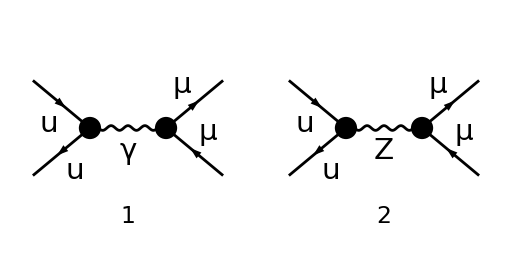

FeynArtsGraphics[][([1] | [2])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

```mathematica
tops = CreateTopologies[0, 2 -> 2];
ins = InsertFields[tops, process];
Paint[ins,ColumnsXRows->{2,1},Numbering->Simple,
SheetHeader->None,ImageSize->{512,256}]
born1=CreateFeynAmp[ins];
```

## Self Energies

```mathematica
tops2 = CreateTopologies[1, 2 -> 2, SelfEnergiesOnly];
ins2 = InsertFields[tops2, process];
ins2 = DiagramSelect[ins2, FreeQ[#, Field[5|6] -> S]&];
Paint[ins2,ColumnsXRows->{11,7},Numbering->Simple,
SheetHeader->None,ImageSize->{1212,756}]
selfff=CreateFeynAmp[ins2];
```

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 10 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 65 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

Restoring 18 field point(s)

in total: 75 Particles insertions

> Top. 1 aebe/cfdf/egfggg.m, 0 diagrams

> Top. 2 aebe/cfdf/egfhghgh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5] | [6] | [7] | [8] | [9] | [10] | [11]
[12] | [13] | [14] | [15] | [16] | [17] | [18] | [19] | [20] | [21] | [22]
[23] | [24] | [25] | [26] | [27] | [28] | [29] | [30] | [31] | [32] | [33]
[34] | [35] | [36] | [37] | [38] | [39] | [40] | [41] | [42] | [43] | [44]
[45] | [46] | [47] | [48] | [49] | [50] | [51] | [52] | [53] | [54] | [55]
[56] | [57] | [58] | [59] | [60] | [61] | [62] | [63] | [64] | [65] | [66]
[67] | [68] | [69] | [70] | [71] | [72] | [73] | [74] | [75] | Null | Null)]

creating amplitudes at level(s) {Particles}

> Top. 1: 10 Particles amplitudes

> Top. 2: 65 Particles amplitudes

in total: 75 Particles amplitudes

## Vertices

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 7 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 8 Particles insertions

> Top. 7: 0 Particles insertions

> Top. 8: 0 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

> Top. 13: 0 Particles insertions

> Top. 14: 0 Particles insertions

> Top. 15: 0 Particles insertions

> Top. 16: 0 Particles insertions

> Top. 17: 0 Particles insertions

> Top. 18: 0 Particles insertions

> Top. 19: 0 Particles insertions

> Top. 20: 0 Particles insertions

> Top. 21: 0 Particles insertions

> Top. 22: 0 Particles insertions

> Top. 23: 0 Particles insertions

> Top. 24: 0 Particles insertions

Restoring 18 field point(s)

in total: 15 Particles insertions

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

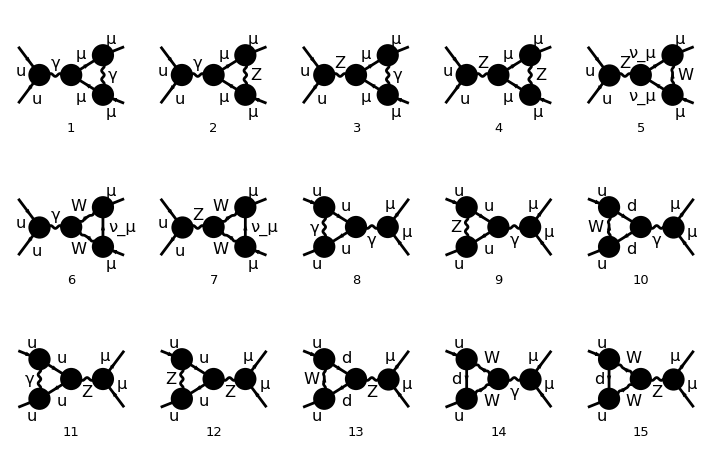

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

creating amplitudes at level(s) {Particles}

> Top. 1: 7 Particles amplitudes

> Top. 2: 8 Particles amplitudes

in total: 15 Particles amplitudes

```mathematica
tops4 = CreateTopologies[1, 2 -> 2, TrianglesOnly];
ins4 = InsertFields[tops4, process];
ins4 = DiagramSelect[ins4, FreeQ[#, Field[5] -> S]&];
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
verttt=CreateFeynAmp[ins4];
```

```mathematica
Paint[ins4,ColumnsXRows->{5,3},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
```

> Top. 1 aebe/cfdg/ehfgfhgh.m, 0 diagrams

> Top. 2 aebf/cgdg/ghefehfh.m, 0 diagrams

-Graphics-

FeynArtsGraphics[][([1] | [2] | [3] | [4] | [5]
[6] | [7] | [8] | [9] | [10]
[11] | [12] | [13] | [14] | [15])]

## Boxes

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 4 Particles insertions

> Top. 8: 5 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

> Top. 11: 0 Particles insertions

> Top. 12: 0 Particles insertions

Restoring 18 field point(s)

in total: 9 Particles insertions

> Top. 1 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 2 aebf/cgdh/efehfggh.m, 0 diagrams

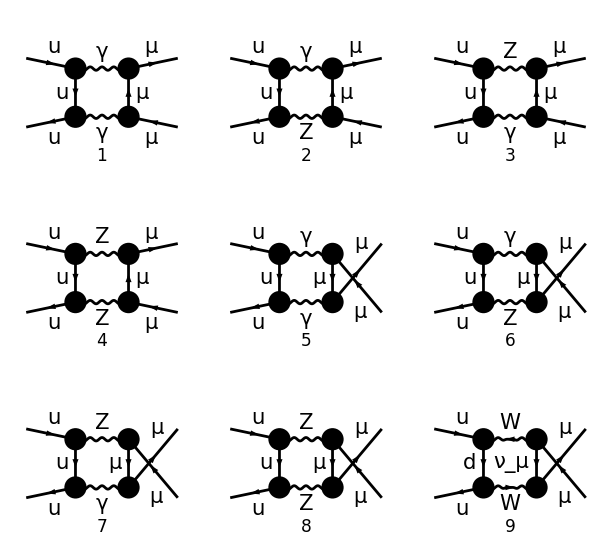

FeynArtsGraphics[][([1] | [2] | [3]
[4] | [5] | [6]
[7] | [8] | [9])]

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 9 Particles amplitudes

```mathematica
tops5 = CreateTopologies[1, 2 -> 2, BoxesOnly];
ins5 = InsertFields[tops5, process];
Paint[ins5,ColumnsXRows->{3,3},Numbering->Simple,
SheetHeader->None,ImageSize->{612,556}]
box1=  CreateFeynAmp[ins5];
```

## Counterterms (CT)

Excluding 18 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

> Top. 5: 0 Particles insertions

> Top. 6: 0 Particles insertions

> Top. 7: 2 Particles insertions

> Top. 8: 4 Particles insertions

> Top. 9: 0 Particles insertions

> Top. 10: 0 Particles insertions

Restoring 18 field point(s)

in total: 8 Particles insertions

> Top. 1 aebe/cfdf/ef.m, 0 diagrams

> Top. 2 aebe/cfdf/ef.m, 0 diagrams

> Top. 3 aebe/cfdf/gegf.m, 0 diagrams

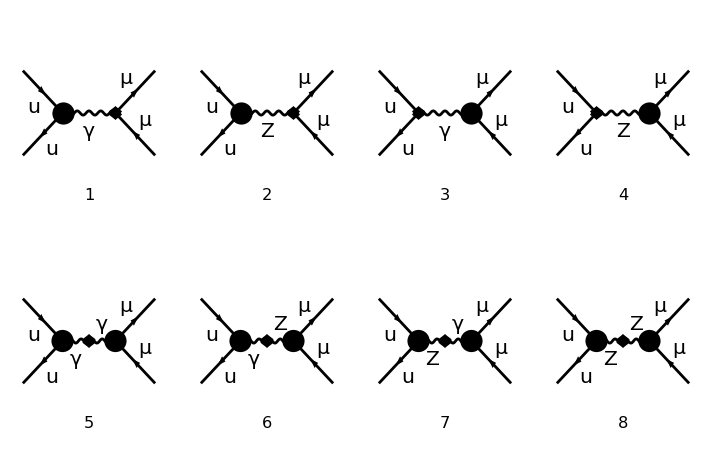

FeynArtsGraphics[][([1] | [2] | [3] | [4]
[5] | [6] | [7] | [8])]

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 4 Particles amplitudes

in total: 8 Particles amplitudes

```mathematica
tops1 = CreateCTTopologies[1, 2 -> 2,
  ExcludeTopologies -> {TadpoleCTs,WFCorrectionCTs (*loop counterterms*)}];
ins1 = InsertFields[tops1, process];
Paint[ins1,ColumnsXRows->{4,2},Numbering->Simple,
SheetHeader->None,ImageSize->{712,456}]
counter = CreateFeynAmp[ins1];
```

## BOX

#### Classificazione

```mathematica
(*in input mettere box1*)
boxtable[box_]:=Module[{b1,b2,b3,samediag,b4,tden,uden,boxcl0,boxcl1},

(*primo metodo: topologie*)
b1=Table[
Which[MemberQ[Part[box,{i}][[1,1]],Topology==1,Infinity],T,
MemberQ[Part[box,{i}][[1,1]],Topology==2,Infinity],U,
True,Print["not identified"]],(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box1]}];

(*secondo metodo*)
(*
tden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,2]]],0];
uden=PropagatorDenominator[Plus[FourMomentum[Incoming,2],FourMomentum[Internal,1],Times[-1,FourMomentum[Outgoing,1]]],0];


boxcl0=Table[boxcl1[i]=Union[Cases[Part[box,{i}][[1,3]]/.MASSES,_FeynAmpDenominator,Infinity]/.FeynAmpDenominator->Sequence],
{i,1,Length[box]}];
Print[boxcl0];

b1=Table[
Which[MemberQ[boxcl1[i],tden,Infinity],T,
MemberQ[boxcl1[i],uden,Infinity],U,True,Null](*,
DeleteCases[boxcl1[i],uden|tden,Infinity]*),
{i,1,Length[box1]}];
*)
(*******************)

b2=Table[
Which[b1[[i]]===T,
{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W]},
b1[[i]]===U,

{Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,2]],QZLl,Infinity],Z,
True,W],
Which[MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QLl,Infinity],γ,
MemberQ[Cases[Part[box,{i}][[1,3]],_FermionChain,Infinity][[2,4]],QZLl,Infinity],Z,
True,W]}
,
True,Print["not identified"]](*identificazione diagrammi t con topology 1 e u con topology 2*)
,(*identificazione diagrammi t con particelle gamma/Z/W in base ai valori delle cariche negli stati finali, l'ordine è up,down. Il caso WW è per esclusione*)

{i,1,Length[box]}];
b3=Table[{i,b1[[i]],b2[[i]]},{i,1,Length[box]}];
Print[b3];
samediag=Gather[b3,Last[#1]==Last[#2]&];
b4=Table[{couple[i]==Last[samediag[[i,1]]],bbox[i]=Cases[samediag[[i]],_Integer,{2}]},{i,1,Length[samediag]}];(*couples:diag t , diag u*)


b4
];
```

```mathematica
boxtable[box1]
```

{{1,T,{γ,γ}},{2,T,{Z,γ}},{3,T,{γ,Z}},{4,T,{Z,Z}},{5,U,{γ,γ}},{6,U,{Z,γ}},{7,U,{γ,Z}},{8,U,{Z,Z}},{9,U,{W,W}}}

{{couple[1]=={γ,γ},{1,5}},{couple[2]=={Z,γ},{2,6}},{couple[3]=={γ,Z},{3,7}},{couple[4]=={Z,Z},{4,8}},{couple[5]=={W,W},{9}}}

```mathematica
Table[totbbox[i]={Part[box1,{bbox[i][[1]]}][[1,3]],Part[box1,{bbox[i][[2]]}][[1,3]]},{i,1,4}];
totbbox[5]=Part[box1,{bbox[5][[1]]}][[1,3]];
```

```mathematica
(*set variabili semplificate*)
mzg=Times[MZ,Power[ZGAUGE,Rational[1,2]]];
mwg=Times[MW,Power[WGAUGE,Rational[1,2]]];
P1=FourMomentum[Incoming,1];
P2=FourMomentum[Incoming,2];
Q1=FourMomentum[Internal,1];
K1=FourMomentum[Outgoing,1];
K2=FourMomentum[Outgoing,2];
```

### Caso box generico:

METTERE MANUALMENTE: totbbox[i]  
totbbox[2][[1]]= BOX1
totbbox[3][[1]]=BOX2

totbbox[2][[2]]=BOX3
totbbox[3][[2]]=BOX4

```mathematica
tboxzz=totbbox[2][[1]]//.MASSES//.{DiracSpinor[Times[-1,P2],x_]->DiracSpinor[P2,x],DiracSpinor[Times[-1,K2],x_]->DiracSpinor[K2,x]}
uboxzz=totbbox[3][[2]]//.MASSES//.{DiracSpinor[Times[-1,P2],x_]->DiracSpinor[P2,x],DiracSpinor[Times[-1,K2],x_]->DiracSpinor[K2,x]}
```

1/(16 π^4)ⅈ v̄[p2,0].((ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)-(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).gs[q1].(-ⅈ EL QUl ga[Lor1].om_--ⅈ EL QUr ga[Lor1].om_+).u[p1,0] ū[k1,0].(-ⅈ EL QLl ga[Lor2].om_--ⅈ EL QLr ga[Lor2].om_+).gs[p2+q1-k2].((ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).v[k2,0] FeynAmpDenominator[1/(q1)^2,1/(-MZ2+(p2+q1)^2),1/(p2+q1-k2)^2,1/(p2+q1-k1-k2)^2] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p2,0].(-ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_--ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).gs[q1].((ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)-(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).u[p1,0] ū[k1,0].(-ⅈ EL QLl ga[Lor4].om_--ⅈ EL QLr ga[Lor4].om_+).gs[-(p2)-q1+k1].((ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)-(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).v[k2,0] FeynAmpDenominator[1/(q1)^2,1/(p2+q1)^2,1/(p2+q1-k1)^2,1/(-MZ2+(p2+q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

```mathematica
(*BORN*)
born=Part[born1,{1}][[1,3]]//.{Index[Lorentz, 1]->Index[Lorentz, bn1],
Index[Lorentz, 2]->Index[Lorentz, bn2]}//.MASSES//.{DiracSpinor[Times[-1,P2],x_]->DiracSpinor[P2,x],DiracSpinor[Times[-1,K2],x_]->DiracSpinor[K2,x]};
bornchains=DeleteCases[Cases[born,_FermionChain,Infinity],_IndexDelta,Infinity];
conjbornchains=CONJ/@Reverse[bornchains,{2}]/.{I->-I,-I->I}
(*colour matrix*)
colourborn=Union[Cases[born,_SumOver|_IndexDelta,Infinity]]
(*born propagators*)
bornpropag=DeleteCases[born, _SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times;
bornpropag2=Collect[numer/@%/.numer->Sequence//Simplify,
PropagatorDenominator[x_,mzg],Simplify]//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)
```

{CONJ[v̄[p1,0].(ⅈ EL QUl ga[Lorbn1].om_-+ⅈ EL QUr ga[Lorbn1].om_+).u[p2,0]],CONJ[ū[k2,0].(ⅈ EL QLl ga[Lorbn2].om_-+ⅈ EL QLr ga[Lorbn2].om_+).v[k1,0]]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

SP[Lorbn1,Lorbn2]/(k1+k2)^2

```mathematica
(*espressioni per calcolare BORN*BOX: *)
```

```mathematica
conjtbox=tboxzz/.FermionChain[x__]:>Reverse[FermionChain[x],{1}]/.{I->-I,-I->I}
conjubox=uboxzz/.FermionChain[x__]:>Reverse[FermionChain[x],{1}]/.{I->-I,-I->I}
```

1/(16 π^4)ⅈ v̄[p1,0].(ⅈ EL QUl ga[Lor1].om_-+ⅈ EL QUr ga[Lor1].om_+).gs[q1].(-(ⅈ EL (I3U-QZUl SW2) IndexDelta[Col1,Col2] ga[Lor3].om_-)/(CW SW)+(ⅈ EL QZUr SW IndexDelta[Col1,Col2] ga[Lor3].om_+)/CW).u[p2,0] ū[k2,0].(-(ⅈ EL (I3L-QZLl SW2) ga[Lor4].om_-)/(CW SW)+(ⅈ EL QZLr SW ga[Lor4].om_+)/CW).gs[p2+q1-k2].(ⅈ EL QLl ga[Lor2].om_-+ⅈ EL QLr ga[Lor2].om_+).v[k1,0] FeynAmpDenominator[1/(q1)^2,1/(-MZ2+(p2+q1)^2),1/(p2+q1-k2)^2,1/(p2+q1-k1-k2)^2] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

1/(16 π^4)ⅈ v̄[p1,0].(-(ⅈ EL (I3U-QZUl SW2) ga[Lor1].om_-)/(CW SW)+(ⅈ EL QZUr SW ga[Lor1].om_+)/CW).gs[q1].(ⅈ EL QUl IndexDelta[Col1,Col2] ga[Lor3].om_-+ⅈ EL QUr IndexDelta[Col1,Col2] ga[Lor3].om_+).u[p2,0] ū[k2,0].(-(ⅈ EL (I3L-QZLl SW2) ga[Lor2].om_-)/(CW SW)+(ⅈ EL QZLr SW ga[Lor2].om_+)/CW).gs[-(p2)-q1+k1].(ⅈ EL QLl ga[Lor4].om_-+ⅈ EL QLr ga[Lor4].om_+).v[k1,0] FeynAmpDenominator[1/(q1)^2,1/(p2+q1)^2,1/(p2+q1-k1)^2,1/(-MZ2+(p2+q1-k1-k2)^2)] g[Lor1,Lor2] g[Lor3,Lor4] SumOver[Col1,3,External] SumOver[Col2,3,External]

#### colour:

```mathematica
(*LOOP DIAGRAM*)

colourf[diag_]:=Module[{input2,fermionchain},
diagram=diag;
(*trace closed fermion loop(if any)*)
tr=Cases[diagram,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input2=DeleteCases[diagram,_MatrixTrace,Infinity]//.MASSES;
fermionchain=Cases[input2,_FermionChain,Infinity];
(*colour traces*)
sunt=Cases[Collect[fermionchain,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];
trsunt=Cases[Collect[tr,_SUNT,Simplify],_SUNT| _IndexDelta,Infinity];(*SUNT in tr*)
sumover=Cases[input2,_SumOver,Infinity];
colour=Join[sunt,trsunt,sumover,colourborn];

colour
];
```

```mathematica
colourf[tboxzz]
colourf[uboxzz]
colourf[wwbox]
colourf[Part[selfff,{4}]]
```

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

{IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External],IndexDelta[Col1,Col2],SumOver[Col1,3,External],SumOver[Col2,3,External]}

«1 more identical outputs»

#### Propagators

```mathematica
(*box t*)
tnumerat=DeleteCases[tboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
(*box u*)
unumerat=DeleteCases[uboxzz, _MatrixTrace |_SumOver | _FermionChain,Infinity]/.FeynAmpDenominator->Times//.FourVector[a__]:>Distribute[FourVector[a]]/.FourVector->SP /.MetricTensor->SP/.PropagatorDenominator[a_,b_]->1/(a^2-b^2)//Simplify
bornpropag2
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (q1)^2 (-MZ2+(p2+q1)^2) (p2+q1-k2)^2 (p2+q1-k1-k2)^2)

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (q1)^2 (p2+q1)^2 (p2+q1-k1)^2 (-MZ2+(p2+q1-k1-k2)^2))

SP[Lorbn1,Lorbn2]/(k1+k2)^2

```mathematica
tnumerat=tnumerat//.MM2->0//.K2->P1+P2-K1
unumerat=unumerat//.MM2->0//.K2->P1+P2-K1
```

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (q1)^2 (-(p1)+q1)^2 (-MZ2+(p2+q1)^2) (-(p1)+q1+k1)^2)

(ⅈ SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4 (q1)^2 (p2+q1)^2 (-MZ2+(-(p1)+q1)^2) (p2+q1-k1)^2)

#### Trace

```mathematica
(*  naive anticommuting gamma5 definitions   *)
myTr[a_,b_] := 4 SP[a,b];
myTr[x__] := Module[{lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
		    lista = {x};
                    ultima = lista[[-1]];
		    menouno = Delete[lista,-1];
		    menodue = Table[ Delete[ menouno, i], {i,1,Length[menouno]}];
		    coefficienti = Table[ (-1)^(i+1) SP[ultima,menouno[[i]] ],
                                          {i,1,Length[menouno]}];
		    nuovetracce = Map[ Apply[ myTr, # ] &, menodue];

                    risultato = coefficienti.nuovetracce;
                    risultato
 ] /; FreeQ[{x},G5] ;
```

```mathematica
myTr[G5,G5] = 4;
myTr[z___,-G5]:=-myTr[z,G5];
myTr[s___,MM,u___]:=MM myTr[s,u];
myTr[x_,G5] = 0;
myTr[x_,y_,G5] = 0;
myTr[x_,y_,z_,G5] = 0;
myTr[x__,G5] := 0 /; OddQ[Length[{x}]] && FreeQ[{x},G5] ;
myTr[a___,G5,b___,G5,c___] := (-1)^Length[{b}]*myTr[a,b,c] /; FreeQ[{b},G5] ;
myTr[a___,G5,b__] := (-1)^Length[{b}]*myTr[a,b,G5] /; FreeQ[Union[{a},{b}],G5] ;
myTr[a1_,a2_,a3_,a4_,G5] =- 4 I myEps[a1,a2,a3,a4];
 myTr[x___,a1_,a2_,a3_,a4_,a5_,a6_,G5] := Module[ {lista,ultima,menouno,menodue,coefficienti,nuovetracce,
                     risultato, i},
  index = Unique[a];
  risultato = myTr[x,a1,a2,a3,a6,G5] SP[a4,a5]-
              myTr[x,a1,a2,a3,a5,G5] SP[a4,a6]+
              myTr[x,a1,a2,a3,a4,G5] SP[a5,a6]+
  I  myTr[x,a1,a2,a3,DiracMatrix[Index[Lorentz,index]]] myEps[a4,a5,a6,Index[Lorentz,index]]; 
  risultato
 ]  /; FreeQ[Union[{x},{a1,a2,a3,a4,a5,a6}],G5] ;
```

```mathematica
(*funzioni prodotto scalare e levicivita*)
SetAttributes[SP,Orderless];
SP/:SP[Index[u__],Index[v__]] SP[p_,Index[u__]] := SP[p,Index[v]];
SP/:SP[a_,Index[mu__]]^2 := SP[a,a];
SP/:SP[a_,Index[mu__]] SP[b_,Index[mu__]] := SP[a,b];
SP/:SP[Index[mu__],Index[mu__]] = d;
SP/:SP[Index[mu__],Index[nu__]]^2 = d;
SP/:SP[-b_,a_]:=-SP[b,a];
SP/:SP[DiracSlash[w_],x_]:=SP[w,x];
SP/:SP[DiracMatrix[w_],x_]:=SP[w,x];
(*levicivita product. 4 indices (d->4)*)
myEps/:myEps[a__]^2:=-Expand@Det@Outer[SP,{a},{a}];
myEps/:myEps[a__] myEps[b__]:=-Expand@Det@Outer[SP,{a},{b}];
```

```mathematica
SP/:SP[P1,P1]:=0;
SP/:SP[P2,P2]:=0;
SP/:SP[K2,K2]:=0;
SP/:SP[K1,K1]:=0;
SP/:SP[P1,P2]:=S/2;
SP/: SP[K1,K2]:=S/2;
SP/: SP[P1,K1]:=(-T)/2;
SP/: SP[P2,K2]:=(-T)/2; 
SP/:SP[P1,K2]:=(-U)/2; 
SP/:SP[P2,K1]:=(-U)/2;
SP/:SP[Q1,Q1]:=Q1^2;
```

```mathematica
(*PROPRIETÀ MYEPS*)
myEps/:myEps[t___,DiracSlash[w_],x___]:=myEps[t,w,x];
myEps/:myEps[t___,DiracMatrix[w_],x___]:=myEps[t,w,x];
myEps /: myEps[a___,Index[Lorentz,mu_],b___] SP[p_,Index[Lorentz,mu_]] := myEps[a,p,b]; 
myEps[a___,b_,c___,b_,d___] := 0
```

```mathematica
move2[a___,ChiralityProjector[pm_],dm:MM|-MM,b___]:=move2[a,dm,ChiralityProjector[pm],b];
move2[a___,ChiralityProjector[pm_],dm:_DiracMatrix|_DiracSlash,b___]:=move2[a,dm,ChiralityProjector[-pm],b];
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=0/;x≠y;
move2[a___,ChiralityProjector[x_],ChiralityProjector[y_],b___]:=move2[a,ChiralityProjector[x],b]/;x==y;
move2[a___,1,b___]:=move2[a,b];
(*move2[a___,DiracSlash[-FourMomentum[p__]],b___]:=-move2[a,DiracSlash[FourMomentum[p]],b];*)
(*NOTA: ANTICOMMUTAZIONE IN D-DIMENSIONI *)
```

```mathematica
trr[s___,MM,u___]:=MM trr[s,u];
trr[s___,-MM,u___]:=-MM trr[s,u];
```

```mathematica
(*calcolo traccia*)
traces[statoi_,statof_]:=Module[{tr0},

(*trace:*)
traceff4[x___, DiracSpinor[z:K2|P2,w_], DiracSpinor[z:K2|P2,w_],y___]:=traceff4[x,(DiracSlash[z]+w),y];
traceff4[ DiracSpinor[z:K2|P2,w_],x__,DiracSpinor[z:K2|P2,w_]]:=traceff4[(DiracSlash[z]+w),x];
traceff4[x___, DiracSpinor[z:K1|P1,w_], DiracSpinor[z:K1|P1,w_],y___]:=traceff4[x,(DiracSlash[z]-w),y];
traceff4[ DiracSpinor[z:K1|P1,w_],x__,DiracSpinor[z:K1|P1,w_]]:=traceff4[(DiracSlash[z]-w),x];
traceff4[a___,-G5,b___]:=- traceff4[a,G5,b];

chargetot=List[chi,chf]//.genericCHZ//.{QUr->QU,QUl->QU,QLl->QL,QLr->QL};
(*stato i*)
tr1i=Table[traceff4[statoi[[i]]/.List->Sequence],{i,1,Length[statoi]}]//.traceff4->move2;(*sposto proiettori in fondo*)
tr1i=tr1i*chargetot[[1]]//.List->Plus//Simplify;(*prova*)
tr2i=Map[Distribute,1/2 tr1i//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];(*sostituisco om+- con espressioni G5 esplicite*)
tr3i=tr2i//.move2->myTr//Expand;


Print["stato i ",1/2 tr1i//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

(*stato f*)
tr0f=Table[traceff4[statof[[i]]/.List->Sequence],{i,1,Length[statof]}];
tr1f=Replace[Table[{Distribute[tr0f[[i]]]},{i,1,Length[tr0f]}],Plus->Sequence,{2},Heads->True]//.traceff4->move2;
tr1f=tr1f*chargetot[[2]]//.List->Plus//Simplify;

tr2f=Map[Distribute,1/2 tr1f//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)},Infinity];
tr3f=tr2f//.move2->myTr//Expand;
(*tr3f=tr2f//.move2->trr//.trr->TR//.TR->myTr//Expand;*)
tr3f=tr3f//.{SP[x__]:>Distribute[SP[x]],myEps[x__]:>Distribute[myEps[x]]}//.myEps[a___,-b_,c___]:>-myEps[a,b,c]//Expand;

Print["stato f ",1/2 tr1f//.{ChiralityProjector[-1]->(1-G5),ChiralityProjector[1]->(1+G5)}];

Return[{tr3i,tr3f}]

];
```

```mathematica
TR[a___,m_,b__,m_,c___] := (-1)^Length[{b}] d TR[a,b,c]+Sum[ma={b}; tmp=Delete[ma,i]; 
(-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;Head[m]===DiracMatrix; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[P2]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K1]; 
TR[a___,m_,b__,m_,c___] := Sum[ma={b}; tmp=Delete[ma,i]; (-1)^(i+1)2SP[ma[[i]],m] TR[a, Sequence @@ tmp, m,c],{i,1,Length[{b}]}]/;m===DiracSlash[K2]; 

TR[]:=1;
TR[s___,MM,u___]:=MM TR[s,u];
TR[s___,-MM,u___]:=-MM TR[s,u];
(*semplification diraslash*)
TR[x___,DiracSlash[-z_],y___]:=-TR[x,DiracSlash[z],y];

TR[x___,DiracSlash[P1],DiracSlash[P1],y___]:=0;
TR[x___,DiracSlash[P2],DiracSlash[P2],y___]:=0;
TR[x___,DiracSlash[K1],DiracSlash[K1],y___]:=0;
TR[x___,DiracSlash[K2],DiracSlash[K2],y___]:=0;
TR[a___,DiracMatrix[Index[Lorentz,m_]],DiracMatrix[Index[Lorentz,m_]], b___] := d TR[a,b];
       
TR[a_,b_]= 4 SP[a,b];
```

NB funzione fermiontrace: calcolo BOX*BORN-> 

tborn1=Table[Map[Distribute,conjbornchains,3][[i]],{i,1,2}];
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];

calcolo BORN*BOX->
tborn1=Table[Map[Distribute,bornchains,3][[i]],{i,1,2}];
stati=Flatten[Table[{Join[tborn3i[[1]],tbi3[[i]]],Join[tborn3i[[2]],tbi3[[i]]]},{i,1,Length[tbi3]}],1];
statf=Flatten[Table[{Join[tborn3f[[1]],tbf3[[i]]],Join[tborn3f[[2]],tbf3[[i]]]},{i,1,Length[tbf3]}],1];

```mathematica
(*input->diag=loop diagram *)
fermiontrace[diag_]:=Module[{tt(*tborn1,tborn2,hb,hbc,tborn3i,tborn3ic,tborn3f,tborn3fc,fermionchain,sti,sti1,tbi,tbic,tbi2,tbi3,tbi3c,stf,stf1,tbf,tbfc,tbf2,tbf3,tbf3c*)},
(*****BORN*****)
tborn1=Table[Map[Distribute,(*bornchains*)conjbornchains,3][[i]],{i,1,2}];
tborn2=Apply[List,tborn1,{1}]/.CONJ->Sequence;
(*seleziono termini per calcolo traccia e cariche*)
hb=Table[Table[Cases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
hbc=Table[Table[DeleteCases[tborn2[[j,i]],_NonCommutative,Infinity],{i,1,Length[tborn2[[j]]]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence,{j,1,2}];
(*STATO I*)
tborn3i=Flatten[Select[hb,MemberQ[#,DiracSpinor[P1,_],Infinity]&],1];
tborn3ic=Flatten[Select[hbc,MemberQ[#,QZUl|QUl,Infinity]&],1];(*charges/coupling*)
(*STATO F*)
tborn3f=Flatten[Select[hb,MemberQ[#,DiracSpinor[K1,_],Infinity]&],1];
tborn3fc=Flatten[Select[hbc,MemberQ[#,QZLl|QLl,Infinity]&],1];(*charges/coupling*)

(*****LOOP DIAGRAM*****)
(*trace closed fermion loop(if any)*)
tr=Cases[diag,_MatrixTrace,Infinity];
(*fermionchain without tr and with external particles masses->0*)
input=DeleteCases[diag,_MatrixTrace,Infinity]//.MASSES;
(*fermionchain part for trace computation*)
fermionchain=DeleteCases[Cases[input,_FermionChain,Infinity],_SUNT|_IndexDelta,Infinity];
(*select fermionchain, expand sums, split state i/f*)
tab1=Table[Distribute[fermionchain[[i]]],{i,1,2}];
(*STATO I*)
sti=Select[tab1,MemberQ[#,DiracSpinor[P1,_],Infinity]&];(*select stato i*)
If[MemberQ[sti,Plus[FermionChain[__],_],Infinity],sti1=Flatten[Apply[List,sti,{1}],1],sti1=sti];(*suddivide in lista se ha piu elementi*)
(*seleziono termini per calcolo traccia e cariche*)
tbi=Table[Cases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbic=Table[DeleteCases[sti1[[i]],_NonCommutative,Infinity],{i,1,Length[sti1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;

tbi2=Table[move2@@tbi[[i]],{i,1,Length[tbi]}]//.move2->List;(*sposto proiettori in fondo a destra con anticommutazione*)
tbi3=DeleteCases[tbi2,0,1];
tbi3c=Delete[tbic,Position[tbi2,0,{1}]];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
(*union diag*born*)
stati=Flatten[Table[{Join[tbi3[[i]],tborn3i[[1]]],Join[tbi3[[i]],tborn3i[[2]]]},{i,1,Length[tbi3]}],1];

(*stati=Flatten[Table[{Join[tborn3i[[1]],tbi3[[i]]],Join[tborn3i[[2]],tbi3[[i]]]},{i,1,Length[tbi3]}],1];*)
chi=Flatten[Table[{Join[tbi3c[[i]],tborn3ic[[1]]],Join[tbi3c[[i]],tborn3ic[[2]]]},{i,1,Length[tbi3c]}],1]//.FermionChain->Times;

(*STATO F*)(*procedimento analogo a STATO I*)
stf=Select[tab1,MemberQ[#,DiracSpinor[K2,_],Infinity]&];
If[MemberQ[stf,Plus[FermionChain[__],_],Infinity],stf1=Flatten[Apply[List,stf,{1}],1],stf1=stf];
tbf=Table[Cases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbfc=Table[DeleteCases[stf1[[i]],_NonCommutative,Infinity],{i,1,Length[stf1]}]//.NonCommutative[a_,b__]:>Sequence[NonCommutative[a],NonCommutative[b]]//.NonCommutative->Sequence;
tbf2=Replace[Table[Distribute[tbf[[i]]//.List->f],{i,1,Length[tbf]}],Plus->Sequence,{2},Heads->True]//.f->move2;
tbf3=DeleteCases[tbf2,0,1]//.move2->List;
If[FreeQ[tbf2,MM,Infinity],
tbf3c=Delete[tbfc,Position[tbf2,0,{1}]],
tbf3c=tbfc];(*semplificazione se ci sono dei termini nulli dove ho om- om+ *)
statf=Flatten[Table[{Join[tbf3[[i]],tborn3f[[1]]],Join[tbf3[[i]],tborn3f[[2]]]},{i,1,Length[tbf3]}],1];

(*statf=Flatten[Table[{Join[tborn3f[[1]],tbf3[[i]]],Join[tborn3f[[2]],tbf3[[i]]]},{i,1,Length[tbf3]}],1];*)
chf=Flatten[Table[{Join[tbf3c[[i]],tborn3fc[[1]]],Join[tbf3c[[i]],tborn3fc[[2]]]},{i,1,Length[tbf3c]}],1]//.FermionChain->Times;

Print["trace closed fermion loop(if any): ",tr];
Return[{stati,statf}]
];
```

```mathematica
genericCHZ={QZLl->QLl,QZUl->QUl,QZDl->QDl,QZLr->QLr,QZUr->QUr,QZDr->QDr};
CHARGEtot={QU->2/3,QL->-1};
sostituzione={SP[Q1,Q1]->Q1^2};
```

#### born*box

```mathematica
boxtt=traces[fermiontrace[conjtbox][[1]],fermiontrace[conjtbox][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i 1/(CW SW)2 ⅈ Alfa EL π QU^2 ((-I3U+QU SW2) move2[gs[p2],ga[Lorbn1],gs[p1],ga[Lor1],gs[q1],ga[Lor3],1-G5]+QU SW2 move2[gs[p2],ga[Lorbn1],gs[p1],ga[Lor1],gs[q1],ga[Lor3],1+G5])

stato f 1/(CW SW)2 ⅈ Alfa EL π QL^2 ((-I3L+QL SW2) move2[gs[k1],ga[Lorbn2],gs[k2],ga[Lor4],gs[p2+q1-k2],ga[Lor2],1-G5]+QL SW2 move2[gs[k1],ga[Lorbn2],gs[k2],ga[Lor4],gs[p2+q1-k2],ga[Lor2],1+G5])

```mathematica
boxuu=traces[fermiontrace[conjubox][[1]],fermiontrace[conjubox][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i 1/(CW SW)2 ⅈ Alfa EL π QU^2 ((-I3U+QU SW2) move2[gs[p2],ga[Lorbn1],gs[p1],ga[Lor1],gs[q1],ga[Lor3],1-G5]+QU SW2 move2[gs[p2],ga[Lorbn1],gs[p1],ga[Lor1],gs[q1],ga[Lor3],1+G5])

stato f 1/(CW SW)2 ⅈ Alfa EL π QL^2 ((-I3L+QL SW2) move2[gs[k1],ga[Lorbn2],gs[k2],ga[Lor2],gs[-(p2)-q1+k1],ga[Lor4],1-G5]+QL SW2 move2[gs[k1],ga[Lorbn2],gs[k2],ga[Lor2],gs[-(p2)-q1+k1],ga[Lor4],1+G5])

#### box*born

```mathematica
boxtt=traces[fermiontrace[tboxzz][[1]],fermiontrace[tboxzz][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i -1/(CW SW)2 ⅈ Alfa EL π QU^2 ((-I3U+QU SW2) move2[gs[p2],ga[Lor3],gs[q1],ga[Lor1],gs[p1],ga[Lorbn1],1-G5]+QU SW2 move2[gs[p2],ga[Lor3],gs[q1],ga[Lor1],gs[p1],ga[Lorbn1],1+G5])

stato f -1/(CW SW)2 ⅈ Alfa EL π QL^2 ((-I3L+QL SW2) move2[gs[k1],ga[Lor2],gs[p2+q1-k2],ga[Lor4],gs[k2],ga[Lorbn2],1-G5]+QL SW2 move2[gs[k1],ga[Lor2],gs[p2+q1-k2],ga[Lor4],gs[k2],ga[Lorbn2],1+G5])

```mathematica
boxuu=traces[fermiontrace[uboxzz][[1]],fermiontrace[uboxzz][[2]]];
```

trace closed fermion loop(if any): {}

trace closed fermion loop(if any): {}

stato i -1/(CW SW)2 ⅈ Alfa EL π QU^2 ((-I3U+QU SW2) move2[gs[p2],ga[Lor3],gs[q1],ga[Lor1],gs[p1],ga[Lorbn1],1-G5]+QU SW2 move2[gs[p2],ga[Lor3],gs[q1],ga[Lor1],gs[p1],ga[Lorbn1],1+G5])

stato f -1/(CW SW)2 ⅈ Alfa EL π QL^2 ((-I3L+QL SW2) move2[gs[k1],ga[Lor4],gs[-(p2)-q1+k1],ga[Lor2],gs[k2],ga[Lorbn2],1-G5]+QL SW2 move2[gs[k1],ga[Lor4],gs[-(p2)-q1+k1],ga[Lor2],gs[k2],ga[Lorbn2],1+G5])

## Semplificazioni/sostituzioni

#### propagatori:

```mathematica
D1=1/List@@Select[tnumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]
D2=1/List@@Select[unumerat,MemberQ[#,FourMomentum,Infinity,Heads->True]&]
```

{(q1)^2,(-(p1)+q1)^2,-MZ2+(p2+q1)^2,(-(p1)+q1+k1)^2}

{(q1)^2,(p2+q1)^2,-MZ2+(-(p1)+q1)^2,(p2+q1-k1)^2}

```mathematica
intdenT[expr_]:=Module[{t,t1,A1},

dennnt=Sort[Table[If[Head[D1[[i]]]===Power,D1[[i,1]]->Sqrt[dn[i]],D1[[i]]->dn[i]],{i,1,Length[D1]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D1]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];
t=ReplaceAllRestricted[expr,dennnt,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENt@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D1]}],{j,1,Length[t]}],
expon=DENt@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D1]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];


intdenU[expr_]:=Module[{t,t1,A2},

dennnu=Sort[Table[If[Head[D2[[i]]]===Power,D2[[i,1]]->Sqrt[dn[i]],D2[[i]]->dn[i]],{i,1,Length[D2]}], Length[#1]>Length[#2] &];
canden=Table[dn[i]->1,{i,1,Length[D2]}];

ReplaceAllRestricted[ex_,rules_List,heads_List]:=ex/.Join[a:Blank[#]:>a&/@heads,rules];(*sostituire solo se certa head*)
t=ReplaceAllRestricted[expr,dennnu,{SP}]//Expand;
If[Head[t]===Plus,
t=List@@t;
expon=Table[DENu@@Table[-1*Exponent[t[[j]],dn[i]],{i,1,Length[D2]}],{j,1,Length[t]}],
expon=DENu@@Table[-1*Exponent[t,dn[i]],{i,1,Length[D2]}]];
t1=t*expon//.canden//.K1+K2->Sqrt[S]//.List->Plus;

t1
];
```

```mathematica
intdenT[tnumerat]
intdenU[unumerat]
```

(ⅈ DENt[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4)

(ⅈ DENu[1,1,1,1] SP[Lor1,Lor2] SP[Lor3,Lor4])/(16 π^4)

```mathematica
kira[expp_]:=Module[{em,t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprod]>0,
If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - *),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t++;If[t>100,Print["ERR"]; Break[]];
];
If[MemberQ[D1,x_+Q1^2,Infinity],
	posq=Position[D1,x_+Q1^2][[1,1]];
	ppq=pp1[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
result=intdenT[expres];

result]
```

```mathematica
ukira[expp_]:=Module[{em,t},
expres=expp;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t=0;
While[Length[tbprod]>0,
If[Length[tbprod]>1,
	tabp=Table[Count[pp1,tbprod[[j]],Infinity],{j,1,Length[tbprod]}];
	pos=Position[tabp,Min[tabp]][[1,1]];
	prod=Cases[expres,SP[__],Infinity][[pos]],
	prod=tbprod[[1]]];

(*definita la rule per sostituire SP*)
For[i=1,i≤Length[pp1],i++,If[MemberQ[pp1[[i]],prod,Infinity],Break[]]];
pp2=pp1[[i]]/.prod->0;
Which[MemberQ[pp1[[i]],Times[-2,prod],Infinity],
	rul= prod->1/2(Subtract@@pp2)(*se prod ha segno - *),
	MemberQ[pp1[[i]],Times[2,prod],Infinity],
	rul=prod->-1/2(Subtract@@pp2)(*se prod ha segno + *)];
expres=expres//.rul;
tbprod=Union[Cases[expres,SP[__],Infinity]];
t++;If[t>100,Print["ERR"]; Break[]];
];
If[MemberQ[D2,x_+Q1^2,Infinity],
	posq=Position[D2,x_+Q1^2][[1,1]];
	ppq=pp1[[posq]]/.Q1^2->0;
	ruleq=Q1^2->-(Subtract@@ppq),ruleq={}];
	expres=expres//.ruleq;
result=intdenU[expres];

result]
```

### box T

```mathematica
boxtt=boxtt//Expand;
```

```mathematica
iep=Select[boxtt[[1]],MemberQ[#,_myEps,Infinity]&];
inep=Select[boxtt[[1]],FreeQ[#,_myEps,Infinity]&];

fep=Select[boxtt[[2]],MemberQ[#,_myEps,Infinity]&];
fnep=Select[boxtt[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Tepsi=iep*tnumerat*bornpropag2//Expand;
```

```mathematica
Teps=ParallelSum[Tepsi[[i]]*fep[[j]]//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//Expand,{i,1,Length[Tepsi]},{j,1,Length[fep]}];
```

```mathematica
(*controllare che l'ordine dei propagatori sia corretto*)
```

```mathematica
D1
```

{(q1)^2,(-(p1)+q1)^2,-MZ2+(p2+q1)^2,(-(p1)+q1+k1)^2}

```mathematica
(*righe da usare solo per box 2*)
q1q2Du=Part[D1,3]
D1=Insert[DeleteCases[D1,q1q2Du],q1q2Du,2]
```

-MZ2+(-(p1)+q1)^2

{(q1)^2,-MZ2+(-(p1)+q1)^2,(p2+q1)^2,(-(p1)+q1+k1)^2}

```mathematica
deninvt=Table[D1[[i]]->dn[i],{i,1,Length[D1]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->0,K2^2->0}
```

{(q1)^2→dn[1],(q1)^2-2 SP[p1,q1]→dn[2],-MZ2+(q1)^2+2 SP[p2,q1]→dn[3],T+(q1)^2-2 SP[p1,q1]+2 SP[q1,k1]→dn[4]}

#### NO myEps

```mathematica
Tneps=inep*fnep*tnumerat*bornpropag2//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//Expand;
```

```mathematica
amplT=Teps+Tneps//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2}//Expand;
```

```mathematica
amplT1=Collect[Map[kira,amplT//.MM2->0],DENt[__],Simplify];
```

#### (*born*box*)

```mathematica
BOX1b=amplT1//.DENt[x__]->bx1[x];
```

```mathematica
rulet3 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx1/kira_bx1.m"];
rult3 = Pick[rulet3, Table[MemberQ[BOX1b, rulet3[[j, 1]], Infinity], {j, 1, Length[rulet3]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX1kirab=Collect[BOX1b/. rult3//.MM2->0//.U->-S-T//.d->4-2ϵ, bx1[__],Simplify];
```

```mathematica
(*****)
```

```mathematica
BOX2b=amplT1//.DENt[x__]->bx2[x];
```

```mathematica
rulet2 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx2/kira_bx2.m"];
rult2= Pick[rulet2, Table[MemberQ[BOX2b, rulet2[[j, 1]], Infinity], {j, 1, Length[rulet2]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX2kirab=Collect[BOX2b/. rult2//.MM2->0//.U->-S-T//.d->4-2ϵ, bx2[__],Simplify];
```

#### (*box*born*)

```mathematica
BOX2=amplT1//.DENt[x__]->bx2[x];
```

```mathematica
rulet2 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx2/kira_bx2.m"];
rult2= Pick[rulet2, Table[MemberQ[BOX2, rulet2[[j, 1]], Infinity], {j, 1, Length[rulet2]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX2kira=Collect[BOX2/. rult2//.MM2->0//.U->-S-T//.d->4-2ϵ, bx2[__],Simplify];
```

```mathematica
(*****)
```

```mathematica
BOX1=amplT1//.DENt[x__]->bx1[x];
```

```mathematica
rulet3 = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx1/kira_bx1.m"];
rult3 = Pick[rulet3, Table[MemberQ[BOX1, rulet3[[j, 1]], Infinity], {j, 1, Length[rulet3]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX1kira=Collect[BOX1/. rult3//.MM2->0//.U->-S-T//.d->4-2ϵ, bx1[__],Simplify];
```

### box U

```mathematica
boxuu=boxuu//Expand;
```

```mathematica
iepu=Select[boxuu[[1]],MemberQ[#,_myEps,Infinity]&];
inepu=Select[boxuu[[1]],FreeQ[#,_myEps,Infinity]&];

fepu=Select[boxuu[[2]],MemberQ[#,_myEps,Infinity]&];
fnepu=Select[boxuu[[2]],FreeQ[#,_myEps,Infinity]&];
```

#### myEps

```mathematica
Uepsi=iepu*unumerat*bornpropag2//Expand;
```

```mathematica
Ueps=ParallelSum[Uepsi[[i]]*fepu[[j]]//Expand,{i,1,Length[Uepsi]},{j,1,Length[fepu]}];
```

#### NO myEps

```mathematica
Uneps=inepu*fnepu*unumerat*bornpropag2//Expand;
```

```mathematica
amplU=Ueps+Uneps//.SP[K2,x_]->SP[P1,x]+SP[P2,x]-SP[K1,x]//.{Alfa->el^2/(4 Pi),Alfa2->el^4/(4 Pi)^2};
```

```mathematica
D2
```

{(q1)^2,(p2+q1)^2,-MZ2+(-(p1)+q1)^2,(p2+q1-k1)^2}

```mathematica
(*usare solo per box 4*)
q1q2Du=Part[D2,3]
D2=Insert[DeleteCases[D2,q1q2Du],q1q2Du,2]
```

-MZ2+(-(p1)+q1)^2

{(q1)^2,-MZ2+(-(p1)+q1)^2,(p2+q1)^2,(p2+q1-k1)^2}

```mathematica
deninvt=Table[D2[[i]]->dn[i],{i,1,Length[D2]}]//Expand;
pp1=deninvt//.{Times[2,a_,b_]->2SP[a,b],Times[-2,a_,b_]->-2SP[a,b],P1^2->0,P2^2->0,K1^2->0,K2^2->0}
```

{(q1)^2→dn[1],-MZ2+(q1)^2-2 SP[p1,q1]→dn[2],(q1)^2+2 SP[p2,q1]→dn[3],U+(q1)^2+2 SP[p2,q1]-2 SP[q1,k1]→dn[4]}

```mathematica
amplU1=Collect[Map[ukira,amplU//.MM2->0//.SP[Q1,Q1]->Q1^2],DENu[__],Simplify]//.MM2->0;
```

#### (*born*box*)

```mathematica
BOX3b=amplU1//.DENu[x__]->bx3[x];
```

```mathematica
rulet3u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx3/kira_bx3.m"];
rult3u = Pick[rulet3u, Table[MemberQ[BOX3b, rulet3u[[j, 1]], Infinity], {j, 1, Length[rulet3u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX3kirab=Collect[BOX3b/. rult3u//.MM2->0//.U->-S-T//.d->4-2ϵ, bx3[__],Simplify];
```

```mathematica
(****)
```

```mathematica
BOX4b=amplU1//.DENu[x__]->bx4[x];
```

```mathematica
rulet2u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx4/kira_bx4.m"];
rult2u = Pick[rulet2u, Table[MemberQ[BOX4b, rulet2u[[j, 1]], Infinity], {j, 1, Length[rulet2u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX4kirab=Collect[BOX4b/. rult2u//.MM2->0//.U->-S-T//.d->4-2ϵ, bx4[__],Simplify];
```

```mathematica
Export["/home/arianna/Scrivania/Università-MAGISTRALE/TESI/tesiQFT/boxgammaZ/BOX4NEW2mixln.txt",BOX4kira];
```

#### (***box*born***)

```mathematica
BOX3=amplU1//.DENu[x__]->bx3[x];
```

```mathematica
rulet3u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx3/kira_bx3.m"];
rult3u = Pick[rulet3u, Table[MemberQ[BOX3, rulet3u[[j, 1]], Infinity], {j, 1, Length[rulet3u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX3kira=Collect[BOX3/. rult3u//.MM2->0//.U->-S-T//.d->4-2ϵ, bx3[__],Simplify];
```

```mathematica
(*****)
```

```mathematica
BOX4=amplU1//.DENu[x__]->bx4[x];
```

```mathematica
rulet2u = Get["/home/arianna/Documenti/kira-2.0/examples/MYEXAMPLE/BOXX/results/bx4/kira_bx4.m"];
rult2u = Pick[rulet2u, Table[MemberQ[BOX4, rulet2u[[j, 1]], Infinity], {j, 1, Length[rulet2u]}]] //.mz2->MZ2//. {s -> S, t -> T}//.MM2->0;
```

```mathematica
BOX4kira=Collect[BOX4/. rult2u//.MM2->0//.U->-S-T//.d->4-2ϵ, bx4[__],Simplify];
```